```mathematica
Needs["NDSolve`FEM`"];
```

```mathematica
ClearAll[ eqn, sol,α,λ,kappa,ρ,Cv, Vw,holePerimeter,Sw, Temp0,Tw,Temp0,r, ϕ, z, x,y,w,rDataMin,rDataMax, phiDataMin, phiDataMax, zDataMin, zDataMax, phiMin, phiMax, rMin, rMax, zMin, zMax, xMin, xMax, yMin, yMax, zMin, zMax,sideOfCopperSquare,L,Ltri,hBeamHole,wBeamHole,lWedge, xCoolingHole, rCooolingHole,phiMinDeg, phiMaxDeg, rad2deg, zHotSpot,powerDensity3D, powerDensityInDegrees3D, cpsInterFunc ] ;
ClearAll[mainDomainRegionEQ, mainDomainRegion, mainMesh, copperBoxRegionEQ, copperBoxSurfaceEQ, copperTopCoolingSlitRegionEQ, copperBotCoolingSlitRegionEQ,copperCoolingSlitRegionEQ,  copperTopCoolingSlitSurfaceEQ, copperBotCoolingSlitSurfaceEQ,copperCoolingSlitSurfaceEQ,copperRightCoolingHoleRegionEQ, copperRightCoolingHoleSurfaceEQ, copperLeftCoolingHoleRegionEQ, copperLeftCoolingHoleRegionEQ, copperLeftCoolingHoleSurfaceEQ, copperCoolingHoleRegionEQ, copperCoolingHoleSurfaceEQ, missingArcRegionEQ, missingArcSurfaceEQ, missingBeamHoleRegionEQ, missingBeamHoleSurfaceEQ];
```

```mathematica
$Assumptions=rMin∈Reals&&rMax>0 && zMin∈Reals && phiMin ∈ Reals  && r ∈ Reals && ϕ ∈ Reals && z ∈ Reals ;
```

```mathematica
cpsInterFunc=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/klcps59_31b_Order1.m"]
```

InterpolatingFunction[{{0.0125, 7.9875}, {-3.11978, 3.11978}, {0.25, 93.75}}, <>]

```mathematica
α=0.0005/1;kappa=0.00385;Temp0=35; ρ=0.001; Cv=4.180; Vw=70;
rDataMin = 0.0125; rDataMax=5.9875; phiDataMin=-3.11978333333; phiDataMax=3.11978333333; zDataMin=0.25; zDataMax=93.75;
sideOfCopperSquare = 2*10;
phiMin=-π; phiMax=π; rMin=0;rMax=sideOfCopperSquare/2*√2; zMin=0; zMax=94; 
xCoolingHole = 7; yCoolingHole=7; rCooolingHole=1.2;Sw=π*rCooolingHole^2;holePerimeter=2*π*rCooolingHole;λ=(ρ*Vw*Sw*Cv)/(α*holePerimeter);
yWedge=2.0;lWedge=3.758770483; phiWedgeMin=7/18*π; phiWedgeMax = 11/18*π;
xMin = -sideOfCopperSquare/2; xMax =sideOfCopperSquare/2; yMin = -sideOfCopperSquare/2; yMax =sideOfCopperSquare/2;
L=zMax;zHotSpot=7; Ltri=54.0;
hBeamHole=1; wBeamHole=1;
rad2deg=N[(180./π)]; phiMinDeg = phiMin * rad2deg; phiMaxDeg = phiMax * rad2deg;
```

```mathematica
powerDensity3D[r_,ϕ_,z_]=Piecewise[{{ cpsInterFunc[r ,ϕ,z],rDataMin≤r≤rDataMax&&phiDataMin≤ϕ≤phiDataMax&& zDataMin≤z≤zDataMax}},0.00000];
```

```mathematica
powerDensityInDegrees3D[r_,ϕ_,z_]:= powerDensity3D[r, ϕ/rad2deg,z];
```

```mathematica
Tw=(ⅇ^(-(z-zMin)/λ))[Temp0+∫_0^((z-zMin)/λ) ⅇ^w Tc[w*λ]ⅆw];
```

```mathematica
(*totalPower = NIntegrate[r*powerDensity3D[r,ϕ,z],{r,rDataMin, rDataMax},{ϕ,phiDataMin,phiDataMax},{z,zDataMin,zDataMax},WorkingPrecision->10]*)
```

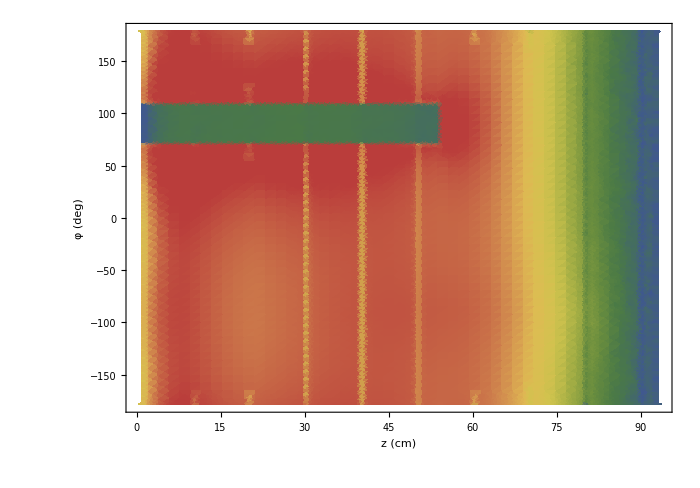

```mathematica
DensityPlot[powerDensityInDegrees3D[0.2, ϕ, z],{z,zMin,zMax},{ϕ,phiMinDeg,phiMaxDeg},ColorFunction->{"DarkRainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{700,500},FrameLabel->{"z (cm)", "φ (deg)",  "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},PlotPoints->50,AspectRatio->0.7]
```

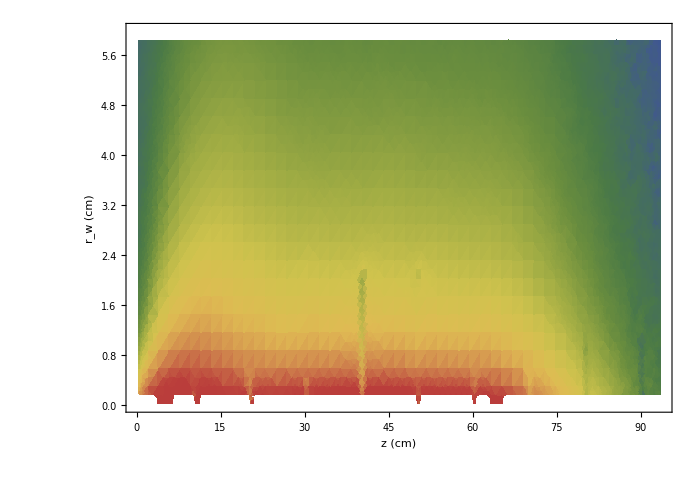

```mathematica
DensityPlot[powerDensityInDegrees3D[r,-120.,z],{z,zMin,zMax},{r,rMin,rMax},ColorFunction->{"DarkRainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{700,500},FrameLabel->{ "z (cm)","r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},PlotPoints->50,AspectRatio->0.7]
```

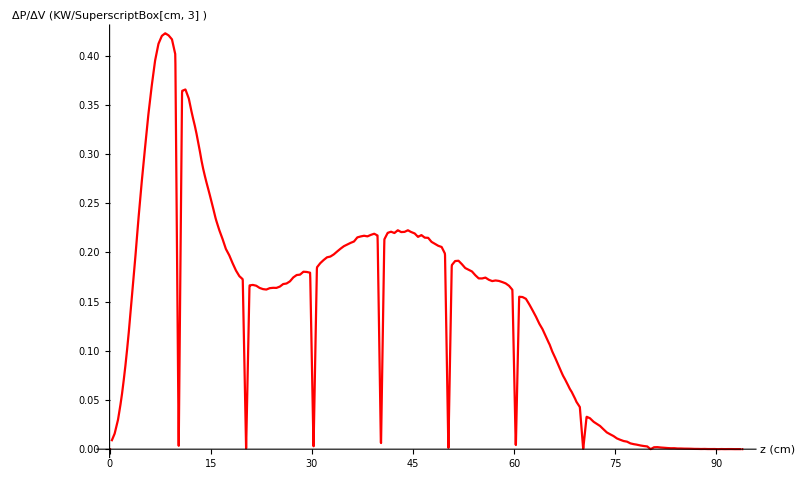

```mathematica
Plot[powerDensityInDegrees3D[0.4,-120.0,z],{z,zMin,zMax}, AxesLabel->{"z (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

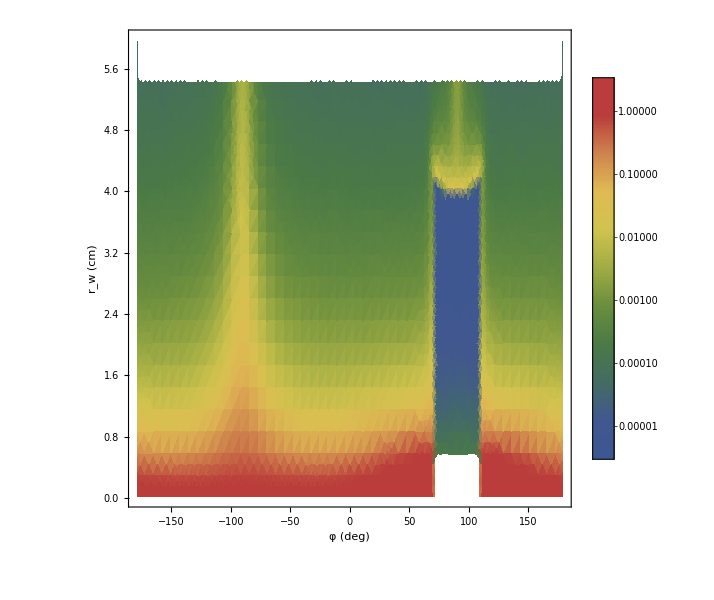

```mathematica
DensityPlot[powerDensityInDegrees3D[r,ϕ,zHotSpot],{ϕ,phiMinDeg,phiMaxDeg},{r,rMin,rMax},ColorFunction->"DarkRainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{600,600},FrameLabel->{"φ (deg)", "r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},PlotPoints->50,AspectRatio->1]
```

```mathematica
(*ParametricPlot3D[{r*Cos[ϕ],r*Sin[ϕ],powerDensity3D[ϕ,r,45]},{r,0,ydat},{ϕ,phiMin,phiMax},ColorFunction->"DarkRainbow",PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},(*PlotRange->{{-ymax,+ymax},{-ymax,+ymax}},*) ImageSize->{600,600},AxesLabel->{"x (cm)","y (cm)"(*,"T (^oC)"*)},(*PlotPoints->{20, 20},*) LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1,ViewPoint->{0,0,Infinity},Axes->{True,True,False},Mesh->None,Lighting->{{"Ambient",White}}]*)
```

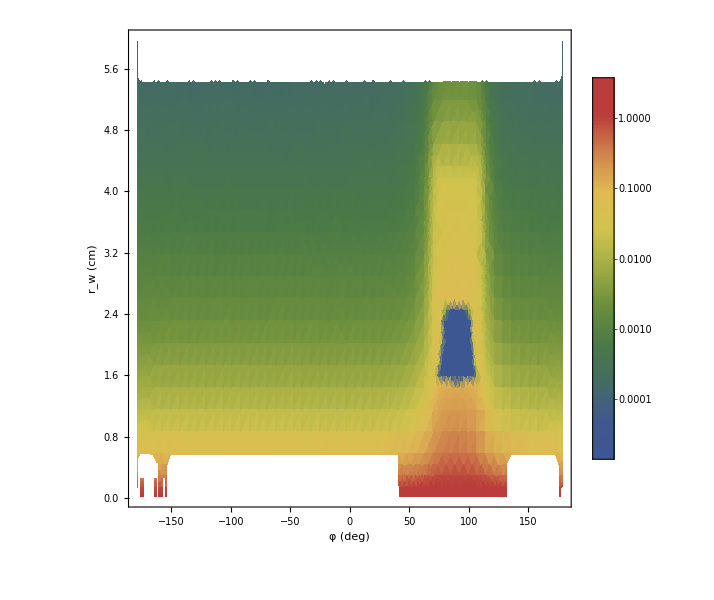

```mathematica
DensityPlot[powerDensityInDegrees3D[r,ϕ,55],{ϕ,phiMinDeg,phiMaxDeg},{r,rMin,rMax},ColorFunction->"DarkRainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{600,600},FrameLabel->{"φ (deg)", "r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},PlotPoints->50,AspectRatio->1]
```

```mathematica
(*ParametricPlot3D[{r*Cos[ϕ],r*Sin[ϕ],powerDensity3D[ϕ,r,55]},{r,0,ydat},{ϕ,phiMin,phiMax},ColorFunction->"DarkRainbow",PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},(*PlotRange->{{-ymax,+ymax},{-ymax,+ymax}},*) ImageSize->{600,600},AxesLabel->{"x (cm)","y (cm)"(*,"T (^oC)"*)},(*PlotPoints->{20, 20},*) LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1,ViewPoint->{0,0,Infinity},Axes->{True,True,False},Mesh->None,Lighting->{{"Ambient",White}}]*)
```

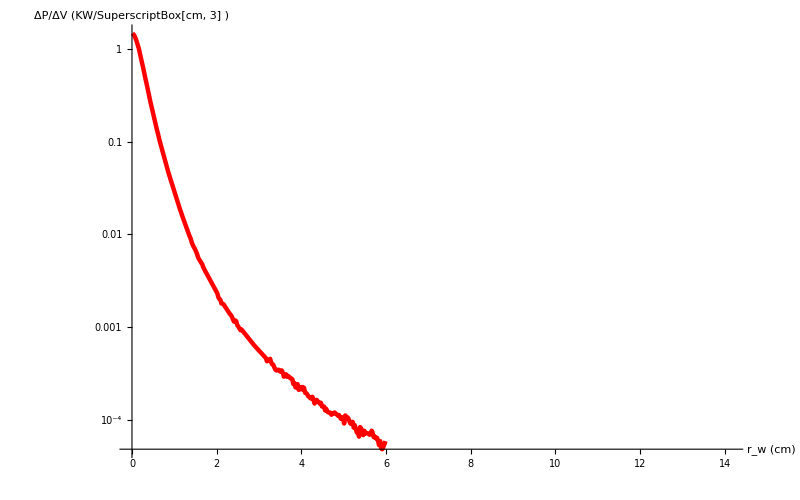

```mathematica
LogPlot[powerDensityInDegrees3D[r,-150.,zHotSpot],{r,rMin,rMax},AxesLabel->{"r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
(*Geometry if the Main Box which is a square *)
```

```mathematica
copperBoxRegionEQ = ((Abs[r*Sin[ϕ]]≤sideOfCopperSquare/2)&&(Abs[r*Cos[ϕ]]≤sideOfCopperSquare/2))&& ( rMin≤r≤rMax ) &&( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
(*RegionPlot3D[copperBoxRegionEQ, {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,zMax}]*)
```

```mathematica
copperBoxSurfaceEQ = (((Abs[r*Sin[ϕ]]==sideOfCopperSquare/2)&&(Abs[r*Cos[ϕ]]≤sideOfCopperSquare/2))||((Abs[r*Sin[ϕ]]≤sideOfCopperSquare/2)&&(Abs[r*Cos[ϕ]]==sideOfCopperSquare/2)))&& ( rMin≤r≤rMax ) && ( phiMin≤ϕ≤phiMax )&& (zMin≤z≤zMax);
```

```mathematica
(*Geometry if the cooling slits on top and the bottom of the main box *)
```

```mathematica
(*RegionPlot3D[copperBoxRegionEQ, {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,zMax}]*)
```

```mathematica
(* Geomtry for the cooling holes on the sides *)
```

```mathematica
copperRightTopCoolingHoleRegionEQ = (((r*Sin[ϕ]-yCoolingHole)^2+(r*Cos[ϕ]-xCoolingHole)^2)<rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperRightTopCoolingHoleSurfaceEQ =(((r*Sin[ϕ]-yCoolingHole)^2+(r*Cos[ϕ]-xCoolingHole)^2)==rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperLeftTopCoolingHoleRegionEQ = (((r*Sin[ϕ]-yCoolingHole)^2+(r*Cos[ϕ]+xCoolingHole)^2)<rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperLeftTopCoolingHoleSurfaceEQ =(((r*Sin[ϕ]-yCoolingHole)^2+(r*Cos[ϕ]+xCoolingHole)^2)==rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperRightBottomCoolingHoleRegionEQ = (((r*Sin[ϕ]+yCoolingHole)^2+(r*Cos[ϕ]-xCoolingHole)^2)<rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperRightBottomCoolingHoleSurfaceEQ =(((r*Sin[ϕ]+yCoolingHole)^2+(r*Cos[ϕ]-xCoolingHole)^2)==rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperLeftBottomCoolingHoleRegionEQ = (((r*Sin[ϕ]+yCoolingHole)^2+(r*Cos[ϕ]+xCoolingHole)^2)<rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperLeftBottomCoolingHoleSurfaceEQ =(((r*Sin[ϕ]+yCoolingHole)^2+(r*Cos[ϕ]+xCoolingHole)^2)==rCooolingHole^2) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&&  (zMin≤z≤zMax);
```

```mathematica
copperCoolingHoleRegionEQ = (copperRightTopCoolingHoleRegionEQ)||(copperLeftTopCoolingHoleRegionEQ) || (copperRightBottomCoolingHoleRegionEQ)||(copperLeftBottomCoolingHoleRegionEQ);
```

```mathematica
copperCoolingHoleSurfaceEQ = (copperRightTopCoolingHoleSurfaceEQ) || (copperLeftTopCoolingHoleSurfaceEQ)||(copperRightBottomCoolingHoleSurfaceEQ) || (copperLeftBottomCoolingHoleSurfaceEQ);
```

```mathematica
(*RegionPlot3D[copperCoolingHoleRegionEQ, {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,zMax}]*)
```

```mathematica
(* Geometry of the triangular arc for the beam channel as defined by Pavel *)
```

```mathematica
missingArcRegionEQ = ( rMin≤r≤rMax ) && ( phiWedgeMin≤ϕ≤phiWedgeMax )&& (zMin≤z≤Ltri)&&(r<(lWedge*Sin[phiWedgeMin]/Sin[ϕ]))  ;
```

```mathematica
(*RegionPlot3D[missingArcRegionEQ, {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,Ltri}]*)
```

```mathematica
missingArcSurfaceEQ = (r==(lWedge*Sin[phiWedgeMin]/Sin[ϕ])||((r<=(lWedge*Sin[phiWedgeMin]/Sin[ϕ]))&&(ϕ==phiWedgeMin||ϕ==phiWedgeMax))) && ( rMin≤r≤rMax ) && ( phiWedgeMin≤ϕ≤phiWedgeMax )&& (zMin≤z≤Ltri);
```

```mathematica
(* Geometry of the square beam channel  that comes after the triangular beam channel *)
```

```mathematica
missingBeamHoleRegionEQ = ((Abs[r*Sin[ϕ]-yWedge]<hBeamHole/2)&&(Abs[r*Cos[ϕ]]<wBeamHole/2)) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&& (Ltri≤z≤zMax);
```

```mathematica
(*RegionPlot3D[missingBeamHoleRegionEQ, {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,Ltri,zMax}]*)
```

```mathematica
missingBeamHoleSurfaceEQ = (((Abs[r*Sin[ϕ]-yWedge]==hBeamHole/2)&&(Abs[r*Cos[ϕ]]≤wBeamHole/2))||((Abs[r*Sin[ϕ]-yWedge]≤hBeamHole/2)&&(Abs[r*Cos[ϕ]]==wBeamHole/2))) && ( rMin≤r≤rMax )&& ( phiMin≤ϕ≤phiMax )&& (Ltri≤z≤zMax);
```

```mathematica
(* Define the main region where the equations will be solved *)
```

```mathematica
mainDomainRegionEQ = (copperBoxRegionEQ)&&  (!missingArcRegionEQ) && (!missingBeamHoleRegionEQ)&&  (!copperCoolingHoleRegionEQ) ;
```

```mathematica
(*RegionPlot3D[mainDomainRegionEQ, {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,zMax}]*)
```

```mathematica
(*mainDomainRegion=ImplicitRegion[ mainDomainRegionEQ,{  r,ϕ,z  }  ] ;*)
```

```mathematica
(*RegionPlot3D[mainDomainRegion]*)
```

```mathematica
(*mainDiscretizedRegion = DiscretizeRegion[ ImplicitRegion[ mainDomainRegionEQ,{   {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,zMax}  }  ], {   {rMin,rMax},{phiMin,phiMax},{zMin,zMax}},  MeshQualityGoal->"Maximal", MaxCellMeasure->{"Length"->0.3}];*)
```

```mathematica
(* Create the mesh which will be used by the solver *)
```

```mathematica
mainMesh=ToElementMesh[DiscretizeRegion[ ImplicitRegion[ mainDomainRegionEQ,{   {r,rMin,rMax},{ϕ,phiMin,phiMax},{z,zMin,zMax}  }  ], {   {rMin,rMax},{phiMin,phiMax},{zMin,zMax}}, MaxCellMeasure->{"Length"->0.23}] ];
```

```mathematica
(*mainMesh=ToElementMesh[ImplicitRegion[ mainDomainRegionEQ,{  r,ϕ,z  }  ] ,MeshQualityGoal->"Maximal",MaxBoundaryCellMeasure->{"Length"->0.05},MaxCellMeasure->{"Length"->0.3}, {{rMin, rMax}, {phiMin, phiMax}, {zMin, zMax}}];*)
```

```mathematica
(*mainMesh["Wireframe"]*)
```

```mathematica
(* Define the equations with boundary conditions and solve them *)
```

```mathematica
eqn=-Laplacian[u[r,ϕ,z],{r,ϕ,z},"Cylindrical"]==1/kappa*powerDensity3D[r,ϕ,z]+ NeumannValue[0.0,missingArcSurfaceEQ] + NeumannValue[0.0,missingBeamHoleSurfaceEQ] + NeumannValue[0.0,copperBoxSurfaceEQ] +NeumannValue[-α/kappa*(u[r,ϕ,z]-(ⅇ^(-(z-zMin)/λ)*(Temp0+∫_0^((z-zMin)/λ) ⅇ^w* u[r,ϕ,w*λ]ⅆw))),copperCoolingHoleSurfaceEQ];
```

```mathematica
(*sol=NDSolveValue[{eqn, u[r,phiMin,z]==u[r,phiMax,z]}, u,{r,ϕ,z} ∈mainMesh];*)
```

```mathematica
(*Export["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_distribution_3D_cps59_4holes_40degC.m", sol]*)
```

```mathematica
(*sol=Import["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_distribution_3D_cps59_4x1.2mmHoles_40degC.m"]*)
```

InterpolatingFunction[{{0., 13.5921}, {-3.14159, 3.14159}, {0., 94.}}, <>]

```mathematica
DensityPlot[sol[r, ϕ/rad2deg,zHotSpot], {ϕ,phiMin*rad2deg,phiMax*rad2deg},{r,rMin,rMax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{Temp0,400},ImageSize->{600,600},FrameLabel->{"φ (deg)", "r_w (cm)", "T (^oC)"} , LabelStyle-> {22,GrayLevel[0],Italic},PlotPoints->200,AspectRatio->1]
```

-Graphics-

```mathematica
ParametricPlot3D[{r*Cos[ϕ],r*Sin[ϕ],sol[r,ϕ,zHotSpot]},{r,rMin,rMax},{ϕ,phiMin,phiMax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{{xMin,xMax},{yMin,yMax},{Temp0,400}},ImageSize->{600,600},AxesLabel->{"x (cm)","y (cm)"(*,"T (^oC)"*)},LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1,ViewPoint->{0,0,Infinity},PlotPoints->200,Axes->{True,True,False},Mesh->None,Lighting->{{"Ambient",White}}]
```

-Graphics3D-

```mathematica
DensityPlot[sol[r, ϕ/rad2deg,55], {ϕ,phiMin*rad2deg,phiMax*rad2deg},{r,rMin,rMax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{Temp0,400},ImageSize->{600,600},FrameLabel->{"φ (deg)", "r_w (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->200,AspectRatio->1]
```

-Graphics-

```mathematica
ParametricPlot3D[{r*Cos[ϕ],r*Sin[ϕ],sol[r,ϕ,55]},{r,rMin,rMax},{ϕ,phiMin,phiMax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{{xMin,xMax},{yMin,+yMax}, {Temp0,300}},ImageSize->{600,600},AxesLabel->{"x (cm)","y (cm)"(*,"T (^oC)"*)},LabelStyle->{24,GrayLevel[0],Italic},AspectRatio->1,ViewPoint->{0,0,Infinity},PlotPoints->200,Axes->{True,True,False},Mesh->None,Lighting->{{"Ambient",White}}]
```

-Graphics3D-

```mathematica
DensityPlot[sol[r, 110/rad2deg,z],{z,zMin,zMax}, {r,rMin,rMax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{Temp0+0,400},ImageSize->{700,500},FrameLabel->{ "z (cm)", "r_w (cm)","T (^oC)"} , LabelStyle-> {22,GrayLevel[0],Italic},PlotPoints->200, AspectRatio->0.7]
```

-Graphics-

```mathematica
DensityPlot[sol[0.2, ϕ/rad2deg,z],{z,zMin,zMax},{ ϕ,phiMin*rad2deg, phiMax*rad2deg} ,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{Temp0,400},ImageSize->{700,500},FrameLabel->{  "z (cm)","φ (deg)","T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->200, AspectRatio->0.7]
```

-Graphics-

```mathematica
SliceContourPlot3D[sol[r, ϕ/rad2deg,z], "CenterPlanes",{r,rMin, rMax},{ϕ,phiMin*rad2deg, phiMax*rad2deg},{z,zMin,zMax}, PlotTheme->"Detailed",PlotRange->Full,  ImageSize->{600,600},PlotLabel->"T (^oC)",AxesLabel->{ "φ (deg)", "r_w (cm)","z (cm)"},LabelStyle->{22GrayLevel[0],Italic}]
```

-Graphics3D-

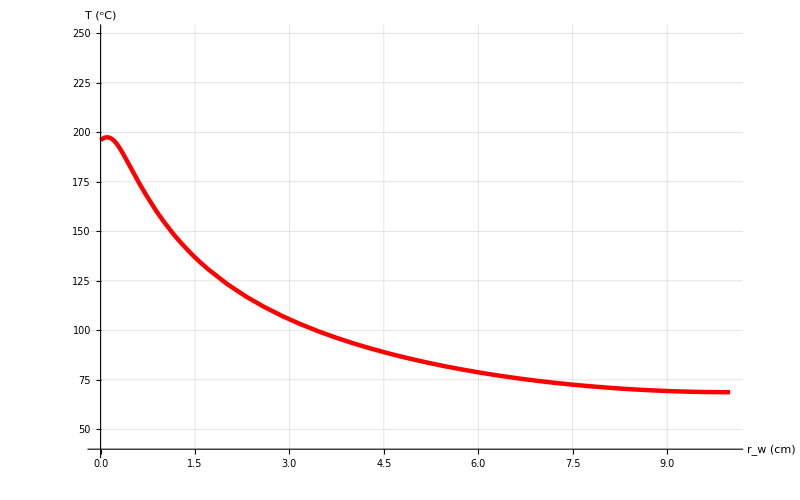

```mathematica
Plot[sol[r, 0/rad2deg,zHotSpot], {r,rMin,rMax},GridLines->Automatic,PlotRange->{Temp0,250},AxesLabel->{"r_w (cm)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

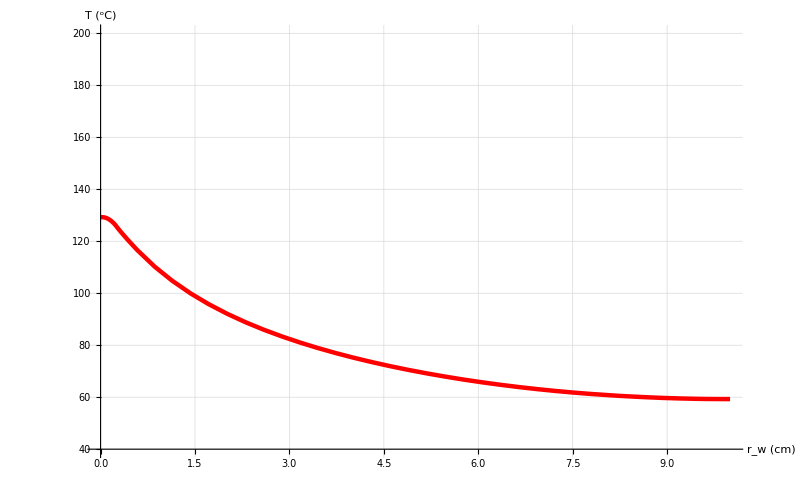

```mathematica
Plot[sol[r, 0/rad2deg,55], {r,rMin,rMax},GridLines->Automatic,PlotRange->{Temp0,200},AxesLabel->{"r_w (cm)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

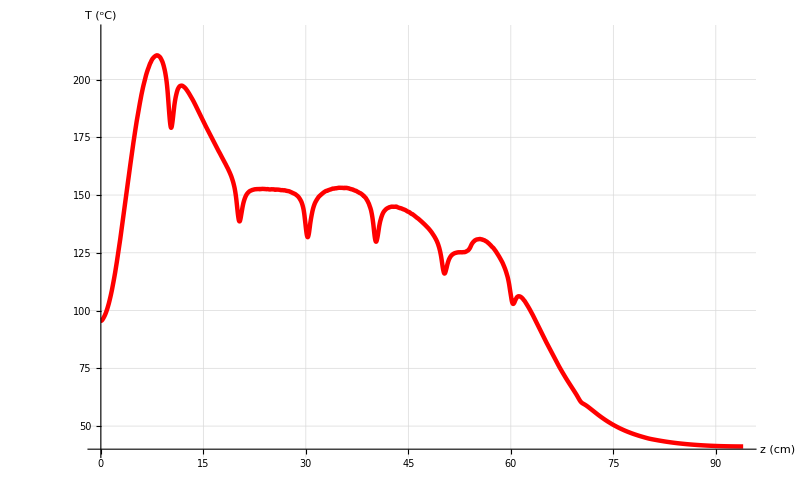

```mathematica
Plot[sol[0.2, 70/rad2deg,z], {z,zMin,zMax},GridLines->Automatic,PlotRange->{Temp0,220},AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

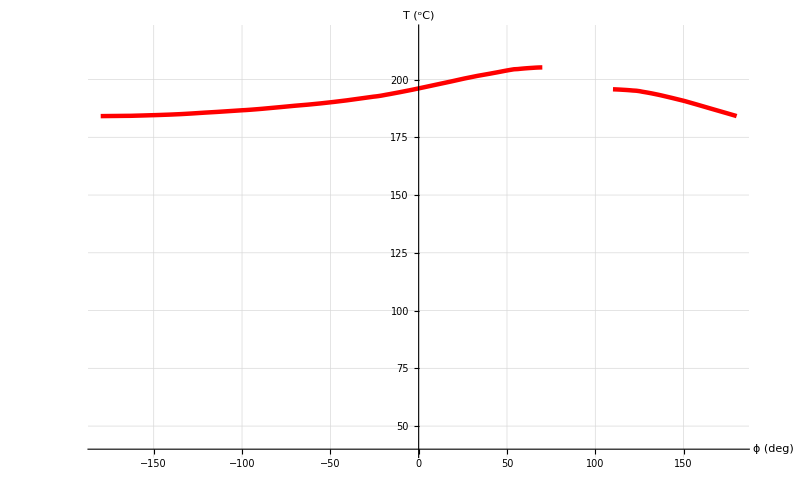

```mathematica
Plot[sol[0.2, ϕ/rad2deg,zHotSpot], {ϕ,phiMin*rad2deg, phiMax*rad2deg},GridLines->Automatic,PlotRange->{Temp0,220},AxesLabel->{"ϕ (deg)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```